# 15 Stability (cont)

Still looking a bit abstract for one more lecture!

## Algorithm 17.1: R.x=b⟶x

### Manual To Start!

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!

```mathematica
Clear[x]
m=4;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
ans = Array[x,m];
b=RandomReal[{-1,1},m];
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
x[4]),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. The last row gives the last value in the answer!

```mathematica
ans⟦-1⟧=b⟦-1⟧/R⟦-1,-1⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
x[3]
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last value in the answer the second last row gives the second last value in the answer.

```mathematica
ans⟦-2⟧=(b⟦-2⟧-R⟦-2,-1⟧*ans⟦-1⟧)/R⟦-2,-2⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
x[2]
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last two values in the answer the third last row gives the third last value in the answer.

```mathematica
ans⟦-3⟧=(b⟦-3⟧-R⟦-3,-2;;-1⟧.ans⟦-2;;-1⟧)/R⟦-3,-3⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(x[1]
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Remember rows are equations. Once you know the last three values in the answer the 4th last row gives the 4th last value in the answer.

```mathematica
ans⟦-4⟧=(b⟦-4⟧-R⟦-4,-3;;-1⟧.ans⟦-3;;-1⟧)/R⟦-4,-4⟧;
Map[MatrixForm,{R,{ans}ᵀ, {b}ᵀ}]
```

{(0.759506 | 0.505934 | 0.825179 | -0.279809
0. | -0.612394 | -0.481638 | 0.487679
0. | 0. | 0.500755 | -0.273192
0. | 0. | 0. | -0.73068),(0.510183
-1.53782
-0.00818474
-0.384286),(-0.289776
0.758287
0.100885
0.28079)}

Looks as though we are done!  We should check we did not mess up!

```mathematica
R.ans-b
```

{1.11022×10^-16,1.11022×10^-16,0.,0.}

### Script

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[x]
m=7;
R=UpperTriangularize[RandomReal[{-1,1},{m,m}]];
MatrixPlot[R,Mesh->All];
b=RandomReal[{-1,1},m];
ans=ConstantArray[0,m];
Do[
ans⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.ans⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}]
Norm[R.ans-b]
```

1.27192×10^-15

### Function

We want to solve the triangular system R.x=b where R is a square upper triangular matrix!  Here is a script.

```mathematica
Clear[AASUTSolve]
AASUTSolve[R_,b_]:= Module[{m=Length[b],x},
(* Alg 17.1 No checking *)
x=ConstantArray[0,m];
Do[
x⟦i⟧=(b⟦i⟧-R⟦i,i+1;;m⟧.x⟦i+1;;m⟧)/R⟦i,i⟧,
{i,m,1,-1}];
x]
```

Testing!

```mathematica
m=7;
R=UpperTriangularize[RandomReal[{0.1,10},{m,m}]];
b=RandomReal[{-1,1},m];
x=AASUTSolve[R,b];
Norm[R.x-b]
```

1.16441×10^-15

## Accuracy/Stability/Backwards Stability

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is stable if  (|| f̃(x) - f(x̃) ||)/(||f(x̃)||)=O(ϵ_machine) for x̃ with (|| x - x̃ ||)/(||x||)=O(ϵ_mac): 
"Stable algorithms give nearly the right answer to nearly the right question!"

f̃ is backwards stable if  f̃(x) = f(x̃) for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

## Floating Point Ops: +, -, ×, ÷, … are backwards stable

This is going to look a bit “picky”!

Let X=ℝ^2 and write X={x_1,x_2}∈X.  Note, x_1 and x_2 are probably not representable floating point numbers. For instance hey could be π or or e or 1/10.

Approximate by floating point numbers i.e.  (x̃)_1=fl(x_1) and (x̃)_2=fl(x_2).  Remember by our floating point axioms (x̃)_1=x_1(1+ϵ_1) and (x̃)_2=x_2(1+ϵ_2) with both ϵ_1 and ϵ_2 less than ϵ_machine.

### FP Subtraction

FP subtract “⊖” the FP numbers and remember that (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)

Combine the bits together  (x̃)_1⊖(x̃)_2=((x̃)_1-(x̃)_2)(1+ϵ_3)=(x_1(1+ϵ_1)-x_2(1+ϵ_2))(1+ϵ_3)

Multiply them all out (x̃)_1⊖(x̃)_2=x_1(1+ϵ_1)(1+ϵ_3)-x_2(1+ϵ_2)(1+ϵ_3)=x_1(1+ϵ_4)-x_2(1+ϵ_5) where ϵ_4=ϵ_1+ϵ_2+ϵ_1 ϵ_2 etc.

Note that |ϵ_4|≤2 ϵ_machine+O(ϵ_machine^2) with the same statement for ϵ_5.

Squint at at this a bit and you see we have all the pieces for backward stability.  We can take C=3.

### Other FP Ops

They all work the same: use the representation; work through the arithmetic; and collect stuff up at the end.

## Examples: Talk about the book examples p109-11

## Wilkinson Polynomial and Eigen Values!

Root finding for polynomials is twitchy. Consider the following “twitchy” polynomial with obvious roots. For some background see https://en.wikipedia.org/wiki/Wilkinson%27s_polynomial

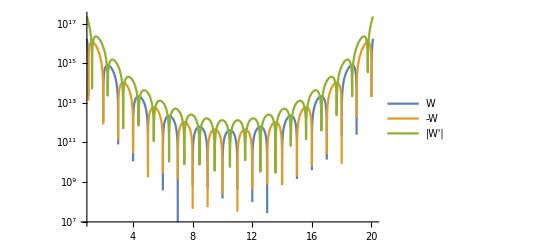

```mathematica
WilkinsonPoly[n_][x_]:=Product[(x-i),{i,1.0,n}]
n=20;
LogPlot[ {WilkinsonPoly[n][x],-WilkinsonPoly[n][x],Abs[WilkinsonPoly[n]'[x]]},{x,0.9,n+0.1},
PlotLegends->{"W","-W","|W'|"}]
```

If I mess with the coefficients just a tiny bit it goes nuts for relatively small n

```mathematica
WilkinsonPoly[20][x]//Expand
```

2.4329×10^18-8.75295×10^18 x+1.38038×10^19 x^2-1.28709×10^19 x^3+8.03781×10^18 x^4-3.59998×10^18 x^5+1.20665×10^18 x^6-3.11334×10^17 x^7+6.30308×10^16 x^8-1.01423×10^16 x^9+1.30754×10^15 x^10-1.35585×10^14 x^11+1.13103×10^13 x^12-7.56111×10^11 x^13+4.01718×10^10 x^14-1.67228×10^9 x^15+5.33279×10^7 x^16-1.25685×10^6 x^17+20615. x^18-210. x^19+x^20

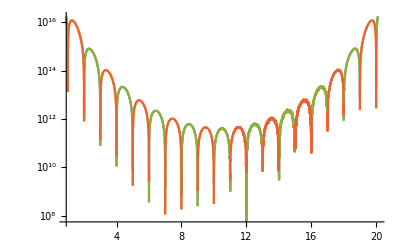

```mathematica
n=20;ϵ=10^-1;
as=CoefficientList[WilkinsonPoly[n][x],x];
bs = as*RandomReal[{1-ϵ,1+ϵ},n+1];
p[cs_][x_]:= Sum[cs[[i]] x^(i-1),{i,Length[cs]}]
LogPlot[ {p[bs][x],-p[bs][x],p[as][x],-p[as][x]},{x,0.9,n+0.1}]
```

The moral of this story is that you can not compute anything that generates the coefficients of even a moderate degree polynomial.

You can not compute eigenvalues by constructing the characteristic polynomial!

In fact, you can (and matlab does) compute polynomial roots by building a matrix!

## Backward Stability and Accuracy

We have an abstract problem f:X→Y with a floating point algorithm f̃:X→Y.

f̃ is accurate if  (|| f̃(x) - f(x) ||)/(||f(x)||)=O(ϵ_mac): 
"Accurate algorithms give nearly the right answer!"

f̃ is backwards stable if  f̃(x) = f(x̃) || for some x̃ satisfying(|| x - x̃ ||)/(||x||)=O(ϵ_machine) 
“Backwards stable algorithm give the right answer to nearly the right question!”

The condition number of f at x∈X is the inherent sensitivity κ(x) of the problem

Theorem 15.1: A backwards stable algorithm f̃ gives relative error O(κ(x)ϵ_machine)
	In symbols,  (|| f̃(x) - f(x) ||)/(||x||)=O(κ(x)ϵ_machine).	
	In practice, the condition number reduces the precision.

This is pretty much exactly what we “think” should happen.

We have a computable "difficulty" for the problem instance "compute f(x)”.  This is the condition number κ(x). It reduces the relative precision of our answer in a predictable way.

For lots of problems the hidden constant in the “bigO” is O(1). In this case log_10 κ(x) is roughly how many decimal digits you lose.

### Work the Proof